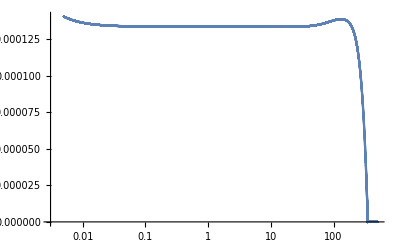

```mathematica
SetDirectory[NotebookDirectory[]];
k=Flatten[Import["./k1.dat"]];
kappa=Flatten[Import["./y13.dat"]];
Zphi=Flatten[Import["./y10.dat"]];
h=Flatten[Import["./y9.dat"]];
etaphi=Flatten[Import["./etaphi.dat"]];
etapsi=Flatten[Import["./etapsi.dat"]];
ListLinePlot[{Transpose[{k,kappa/k}]},ScalingFunctions->{"Log",Automatic},PlotRange->{All,All}]
```

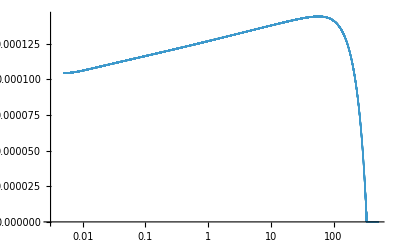

```mathematica
ListPlot[Transpose[{k,kappa/(Zphi k)}],ScalingFunctions->{"Log",Automatic}]
```

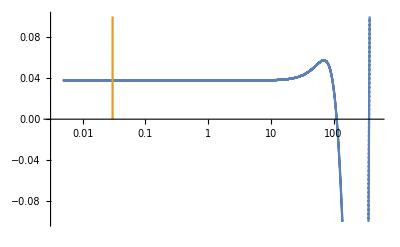

```mathematica
ListLinePlot[{Transpose[{k,etaphi}],{{0.03,0},{0.03,1}}},ScalingFunctions->{"Log",Automatic},PlotRange->{All,{-0.1,0.1}}]
```

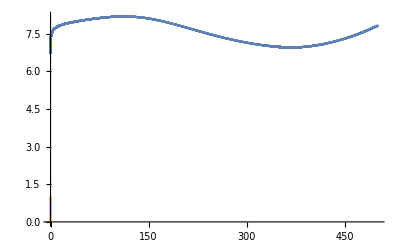

```mathematica
ListLinePlot[{Transpose[{k,h}],{{0.03,0},{0.03,1}}},ScalingFunctions->{Automatic,Automatic},PlotRange->{All,All}]
```

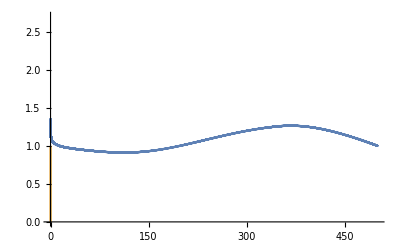

```mathematica
ListLinePlot[{Transpose[{k,Zphi}],{{0.03,0},{0.03,1}}},ScalingFunctions->{Automatic,Automatic},PlotRange->{All,{0,2.7}}]
```